## DropPerpendicular-example.nb

Example Cellzilla2D notebook.

GPL License applies. 
See http://xlr8r.info and http://cellzilla.info for further details.

```mathematica
<<Cellzilla2D.m
```

Cellzilla2D (2.3.6 (9-Nov-2012)) loaded Fri 9 Nov 2012 07:05:21
using xCellerator 0.90 and XSSA 1204002

```mathematica
APoint={1,1}; 
ALineSegment={{2,4}, {3, -1}}; 
AnotherPoint={2,-1.7};
```

```mathematica
intersectionPoint=DropPerpendicular[APoint,ALineSegment]
```

{33/13,17/13}

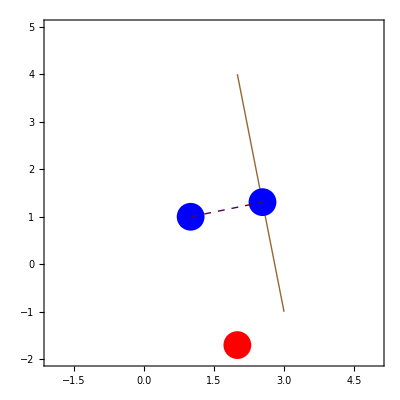

```mathematica
Show[Graphics[{
Blue, PointSize[.05], Point[APoint], 
Brown,Thick,
Line[ALineSegment],
Blue,
Point[intersectionPoint], 
Darker[Purple], Dashed, 
Line[{APoint, intersectionPoint}],
Red, Point[AnotherPoint]}], Frame-> True, PlotRange-> {{-2,5}, {-2, 5}}, AspectRatio-> 1, Axes-> True]
```

Returns $Failed if the perprendicular from the point to the line segment does not intersect the line segment.

```mathematica
DropPerpendicular[AnotherPoint, ALineSegment]
```

$Failed

With the 3rd argument set to True, it will find as close a perpendicular as possible, by sliding the result to the nearest endpoint.

```mathematica
DropPerpendicular[AnotherPoint, ALineSegment, True]
```

{3,-1}